```mathematica
names={"prog1.txt","prog2.txt","prog3.txt"};
imp=Table[Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>names[[i]],"Table"],{i,1,Length[names]}];
data=imp
```

{{{510.38,20648.4},{511.39,21416.2},{512.31,22169.8},{513.12,22594.8},{514.23,24139.3},{515.55,24918.6},{516.75,25676.8},{518.06,26152.2},{519.36,27342.},{520.86,28514.8},{522.45,28514.1},{524.03,30137.6},{525.52,31489.5},{527.29,32406.1},{528.95,33866.4},{530.91,36006.5},{532.95,36370.8},{534.88,37365.},{536.81,38085.2},{539.11,37937.6},{541.3,37900.8},{543.48,38449.9},{545.74,39060.8},{548.18,40202.9},{550.78,41168.5},{553.37,43897.2},{556.22,43105.3},{558.86,43389.9},{561.84,44442.5},{564.62,44223.9}},{{545.27,40795.2},{547.43,42538.1},{549.95,43011.8},{552.36,43579.},{554.75,43685.8},{557.31,43573.6},{559.86,44733.5},{562.74,43093.5},{565.51,42056.3},{568.53,41244.5},{571.61,40516.4},{574.74,39839.5},{578.1,38753.1},{581.6,38001.},{584.97,37887.3},{588.39,36955.},{592.1,37770.3},{595.84,37995.2},{599.77,39063.6},{603.56,39868.5},{607.45,40721.4},{611.58,41522.3}},{{569.41,44092.},{572.13,42262.5},{575.35,40850.6},{578.45,39297.2},{581.77,38222.6},{585.23,38104.4},{588.64,37136.5},{592.1,37770.3},{595.84,37995.2},{599.61,38881.9},{603.4,39959.7},{607.45,40721.4},{611.43,41704.9}}}

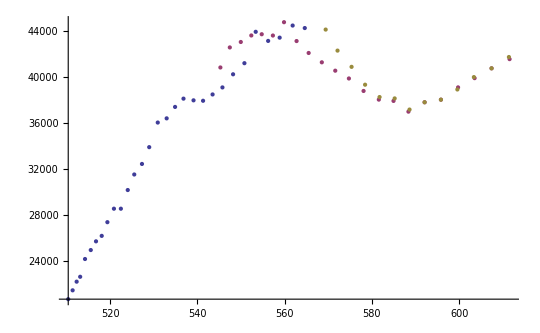

```mathematica
ListPlot[data]
```

{{47,510.38},{46,511.39},{45,512.31},{44,513.12},{43,514.23},{42,515.55},{41,516.75},{40,518.06},{39,519.36},{38,520.86},{37,522.45},{36,524.03},{35,525.52},{34,527.29},{33,528.95},{32,530.91},{31,532.95},{30,534.88},{29,536.81},{28,539.11},{27,541.3},{26,543.48},{25,545.74},{24,548.18},{23,550.78},{22,553.37},{21,556.22},{20,558.86},{19,561.84},{18,564.62}}

{{28,545.27},{27,547.43},{26,549.95},{25,552.36},{24,554.75},{23,557.31},{22,559.86},{21,562.74},{20,565.51},{19,568.53},{18,571.61},{17,574.74},{16,578.1},{15,581.6},{14,584.97},{13,588.39},{12,592.1},{11,595.84},{10,599.77},{9,603.56},{8,607.45},{7,611.58}}

{{21,569.41},{20,572.13},{19,575.35},{18,578.45},{17,581.77},{16,585.23},{15,588.64},{14,592.1},{13,595.84},{12,599.61},{11,603.4},{10,607.45},{9,611.43}}

C:\fpgithub\0916-I2\data\prog1nl.txt

C:\fpgithub\0916-I2\data\prog2nl.txt

C:\fpgithub\0916-I2\data\prog3nl.txt

{{47,19593.2},{46,19554.5},{45,19519.4},{44,19488.6},{43,19446.6},{42,19396.8},{41,19351.7},{40,19302.8},{39,19254.5},{38,19199.},{37,19140.6},{36,19082.9},{35,19028.8},{34,18964.9},{33,18905.4},{32,18835.6},{31,18763.5},{30,18695.8},{29,18628.6},{28,18549.1},{27,18474.},{26,18399.9},{25,18323.7},{24,18242.2},{23,18156.1},{22,18071.1},{21,17978.5},{20,17893.6},{19,17798.7},{18,17711.}}

{{28,18339.5},{27,18267.2},{26,18183.5},{25,18104.1},{24,18026.1},{23,17943.3},{22,17861.6},{21,17770.2},{20,17683.2},{19,17589.2},{18,17494.4},{17,17399.2},{16,17298.},{15,17193.9},{14,17094.9},{13,16995.5},{12,16889.},{11,16783.},{10,16673.1},{9,16568.4},{8,16462.3},{7,16351.1}}

{{21,17562.},{20,17478.5},{19,17380.7},{18,17287.6},{17,17188.9},{16,17087.3},{15,16988.3},{14,16889.},{13,16783.},{12,16677.5},{11,16572.8},{10,16462.3},{9,16355.1}}

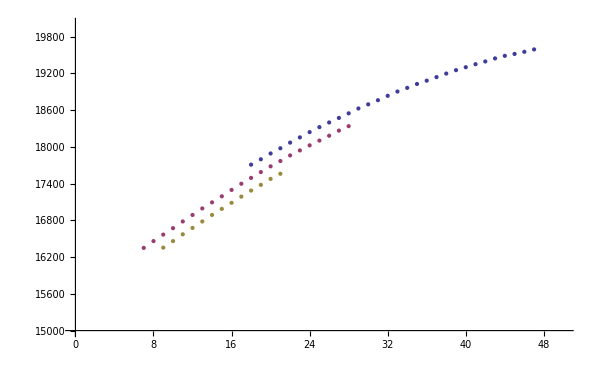

```mathematica
ν0=Table[{48-i,data[[1,i,1]]},{i,1,Length[data[[1]]]}]
ν1=Table[{29-i,data[[2,i,1]]},{i,1,Length[data[[2]]]}]
ν2=Table[{22-i,data[[3,i,1]]},{i,1,Length[data[[3]]]}]

Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog1nl.txt",ν0,"Table"]
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog2nl.txt",ν1,"Table"]
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>"prog3nl.txt",ν2,"Table"]
ν0[[All,2]]=10^7/ν0[[All,2]];
ν1[[All,2]]=10^7/ν1[[All,2]];
ν2[[All,2]]=10^7/ν2[[All,2]];
ν0
ν1
ν2

ListPlot[{Tooltip[ν0],Tooltip[ν1],Tooltip[ν2]},PlotRange->{{0,50},{15000,20000}}]
```

```mathematica
ν0[[20]]
ν1[[1]]
ν1[[8]]
ν2[[1]]
```

{28,18549.1}

{28,18339.5}

{21,17770.2}

{21,17562.}

```mathematica
G12=Table[ν0[[i+19,2]]-ν1[[i,2]],{i,1,11}]
G12m=Mean[G12]
StandardDeviation[G12]
G23=Table[ν1[[i+7,2]]-ν2[[i,2]],{i,1,13}]
G23m=Mean[G23]
StandardDeviation[G23]

2*G12m-G23m
1/2*(G12m-G23m)
```

{209.552,206.868,216.47,219.609,216.045,212.735,209.483,208.302,210.416,209.44,216.581}

212.318

4.19587

{208.158,204.608,208.497,206.867,210.248,210.746,205.636,205.855,212.501,211.532,210.275,210.798,213.259}

209.152

2.76865

215.484

1.58305

#### Bestimmung Dissotiationsenergie Angeregter Zstd mit Morse - Potential

```mathematica
215.484^2/(4 * 1.58305)
```

7332.89

```mathematica
15769+4392-7603
```

12558